```mathematica
Clear["Global`*"]
Column@NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"mathematica_plot_options.nb"}]];
(*インポート*)
lenNode=5;
filename=FileNameJoin[{NotebookDirectory[],"output","result_"<>ToString[lenNode]<>".json"}]
jsonInfo[filename]
data=Import[filename];
{time,timeModal,displacement,displacementModal,velocity,velocityModal,modeshape,freq,omega,M,K}={"time","time_modal","displacement","displacement_modal","velocity","velocity_modal","mode_shape","freq",Sqrt["freq"],"M","K"}/.data;
```

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_ODE/output/result_5.json

no. | title | length
1 | K | 5
2 | M | 5
3 | displacement | 5001
4 | displacement_modal | 5001
5 | freq | 5
6 | mode_shape | 5
7 | time | 5001
8 | time_modal | 5001
9 | velocity | 5001
10 | velocity_modal | 5001

## 厳密解

```mathematica
(*Clear[{L,λ,b,h,ρ,yong,i,ω}];*)
L=0.9;
λ={1.8751040687119611,4.694091132974174,7.854757438237613,10.995540734875467,14.13716839104647};

b=0.01;
h=0.005;

A=b*h;
ρ=7.668*1000;
yong=205*10^9;
i=(b*h^3)/12;
fExact=(λ/L)^2*Sqrt[yong*i/(ρ*A)]/(2π)
```

{5.15586,32.3112,90.4724,177.29,293.073}

## モード解析

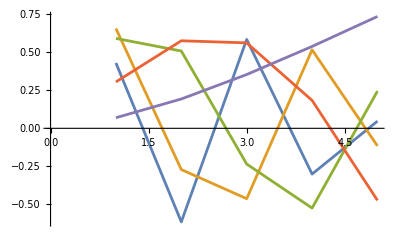

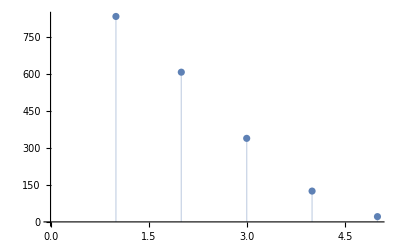

```mathematica
(*Mathematicaの関数で固有値問題を解く*)
{λ,v}=Eigensystem[{K,M}];
ListPlot[v[[;;]],Joined->True]
ListPlot[Sqrt[λ],Filling->Bottom]
```

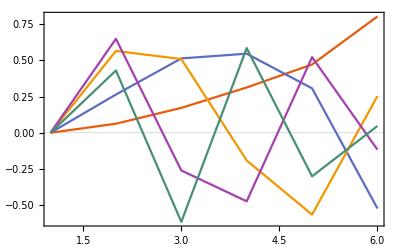

```mathematica
(*c++でQR分解などを駆使して固有値問題を解く*)
shape=Table[Prepend[(Transpose@modeshape)[[i]],0],{i,lenNode,1,-1}];
ListPlot[shape[[1;;lenNode]]
,PlotRange->{{1,All},All}
,Joined->True
,Evaluate[plot2Doption]]
```

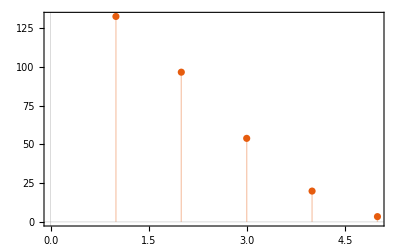

```mathematica
ListPlot[omega/(2π),Filling->Bottom,Joined->False,Evaluate[plot2Doption]]
```

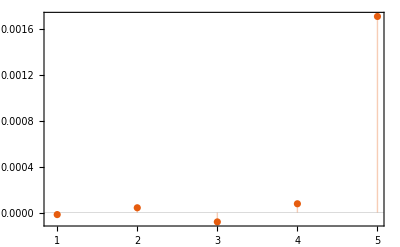

```mathematica
(*ある節点の変位のチェック*)
ListPlot[displacementModal[[1000]],Joined->False,Filling->Axis,PlotRange->All,Evaluate[plot2Doption]]
```

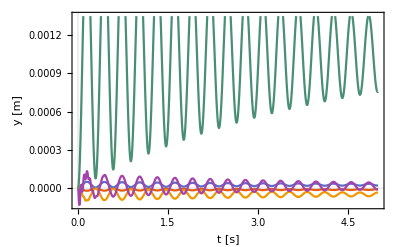

```mathematica
(*ある節点のモード振幅のチェック*)
ListPlot[Table[{timeModal[[t]],displacementModal[[t]][[n]]},{n,1,5},{t,1,Length[timeModal]}],FrameLabel->{"t [s]","y [m]"},Evaluate[plot2Doption]]
```

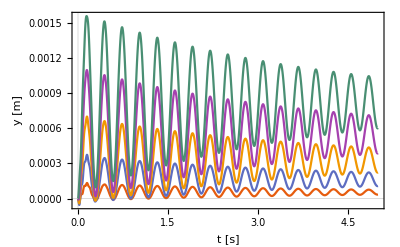

```mathematica
(*ある節点の変位のチェック*)
sum[t_]:=Dot[modeshape,displacementModal[[t]]];
ListPlot[Table[{timeModal[[t]],sum[t][[n]]},{n,1,lenNode},{t,1,Length[timeModal]}],FrameLabel->{"t [s]","y [m]"},Evaluate[plot2Doption]]
```

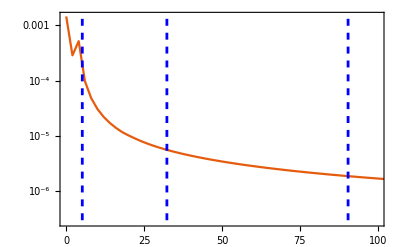

```mathematica
indexstart=500;
indexend=1000;
plotdata=Table[{timeModal[[t]],sum[t][[n]]},{n,1,lenNode},{t,1,Length[timeModal]}][[-1]];
{plottime,plotvalue}=Transpose[plotdata[[indexstart;;indexend]]];
ListLogPlot[interpolateAndFourier[plottime,plotvalue]
,Epilog->{Blue,Dashed,Thickness[0.005],Table[Line[{{x,-100},{x,1}}],{x,fExact}]}
,PlotRange->{{0,100},All}
,Joined->True
,GridLines->Automatic
,Evaluate[plot2Doption]]
```

```mathematica
(*全節点の変位のチェック*)
Animate[
ListPlot[Table[{sum[t][[i]],i/lenNode},{i,1,lenNode}]
,PlotMarkers->Automatic
,PlotRange->{0.01*{-1,1},{-0.1,1}}
,FrameLabel->{"x [m]","y [m]"}
,Evaluate[plot2Doption]
,PlotLabel->Style["StyleBox[\"T\",FontSlant->\"Italic\"]="<>ToString@timeModal[[t]]]
,Joined->True
,AspectRatio->1.5]
,{t,1,Length[displacement],10}]
(*Export["~/Desktop/temp.gif",%]*)
```

## 動的解析

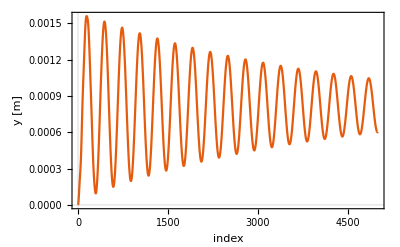

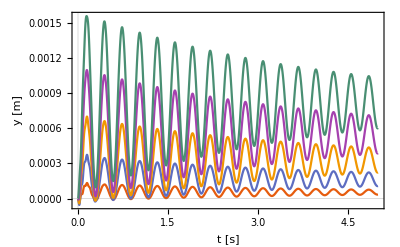

```mathematica
(*ある節点の変位のチェック*)
ListPlot[plotdata=Table[{i,displacement[[i,-1]]},{i,1,Length[time]}],FrameLabel->{"index","y [m]"},Evaluate[plot2Doption]]
ListPlot[Table[{time[[i]],displacement[[i,n]]},{n,1,lenNode},{i,1,Length[time]}],FrameLabel->{"t [s]","y [m]"},Evaluate[plot2Doption]]
```

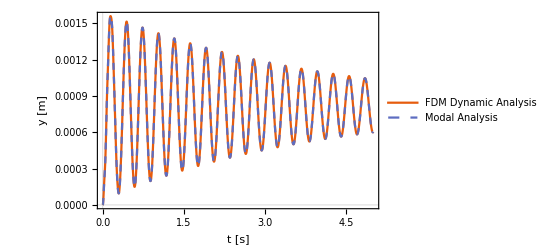

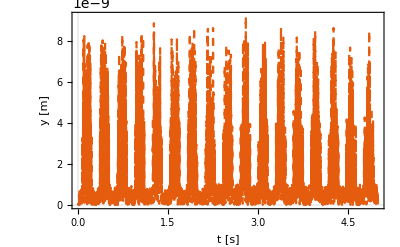

```mathematica
ListPlot[
{
plotdata=Table[{time[[i]],displacement[[i,-1]]},{i,1,Length[time]}],
Table[{timeModal[[i]],sum[i][[-1]]},{i,1,Length[timeModal]}]}
,PlotStyle->{Automatic,Dashed}
,FrameLabel->{"t [s]","y [m]"}
,PlotLegends->{"FDM Dynamic Analysis","Modal Analysis"}
,Evaluate[plot2Doption]]

ListPlot[
Table[{time[[i]],Abs[displacement[[i,-1]]-sum[i][[-1]]]},{i,1,Length[time]}]
,PlotRange->All
,PlotStyle->{Automatic,Dashed}
,FrameLabel->{"t [s]","y [m]"}
,Evaluate[plot2Doption]]
```

```mathematica
(*全節点の変位のチェック*)
Animate[
ListPlot[Table[{displacement[[t,i]],i/lenNode},{i,1,lenNode}]
,PlotMarkers->Automatic
,PlotRange->{0.01*{-1,1},{-0.1,1}}
,FrameLabel->{"x [m]","y [m]"}
,Evaluate[plot2Doption]
,PlotLabel->Style["StyleBox[\"T\",FontSlant->\"Italic\"]="<>ToString@time[[t]]]
,Joined->True
,AspectRatio->1.5]
,{t,1,Length[displacement],10}]
(*Export["~/Desktop/temp.gif",%]*)
```

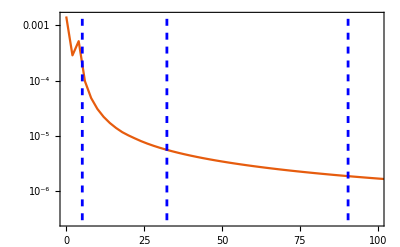

```mathematica
(*フーリエ変換で固有振動数をチェック*)
(*indexstart=1000;
indexend=2000;*)
indexstart=500;
indexend=1000;
{plottime,plotvalue}=Transpose[plotdata[[indexstart;;indexend]]];
ListLogPlot[interpolateAndFourier[plottime,plotvalue]
,Epilog->{Blue,Dashed,Thickness[0.005],Table[Line[{{x,-100},{x,1}}],{x,fExact}]}
,PlotRange->{{0,100},All}
,Joined->True
,GridLines->Automatic
,Evaluate[plot2Doption]]
```

```mathematica
(*SDOF*)
```